Charles Rambo

# Optical Design 1: Geometric Optics

## Homework Problems

## Problem 1: Ray tracing through a plano-convex conic-section lens

Consider meridional ray tracing through a thick lens with front surface z(y) = 1/2cy^2 and a planar back surface a z = d. Assume that a ray propagating in the direction of the z-axis enters the system at height y. Write a code for calculating the position of the crossing point of the output ray with the optical axis. Assuming that c = 1/(50 mm), d = 10 mm, and that the lens with a refractive index n = 1.5 is surrounded by air in both sides, study the position of the crossing point when y increases from, e.g., zero to 20 mm. Then repeat the analysis for a lens with a spherical front surface. You will find that spherical aberration is over-corrected for the paraboloid but under-corrected for the spherical surface. Finally, try looking for an optimum elliptical front surface by varying the parameter ϵ between zero and one.

```mathematica
c=1/50;d=10;ng=1.5;na=1;R=1/c;y={0.0001, 5, 10, 15, 20};n1=na;n2=ng;n3=na;ϵ=1;ϵideal={0,0.25,0.5,0.75,1};
```

```mathematica
z1=1/2*c*y^2
z2=(c*y^2)/(1+√(1-ϵ*c^2*y^2))
```

{1.×10^-10,1/4,1,9/4,4}

{1.×10^-10,1/(2 (1+(3 √11)/10)),2/(1+(2 √6)/5),9/(2 (1+(√91)/10)),8/(1+(√21)/5)}

```mathematica
lpar=(y-Tan[ArcTan[c*y]-ArcSin[n1/n2*Sin[ArcTan[c*y]]]]/(d-z1))/Tan[ArcSin[n2/n3*Sin[ArcTan[c*y]-ArcSin[n1/n2*Sin[ArcTan[c*y]]]]]]+d
lcirc=(y-Tan[ArcTan[c*y]-ArcSin[n1/n2*Sin[ArcTan[c*y]]]]/(d-z2))/Tan[ArcSin[n2/n3*Sin[ArcTan[c*y]-ArcSin[n1/n2*Sin[ArcTan[c*y]]]]]]+d
```

{109.933,109.973,110.091,110.282,110.532}

{109.933,109.973,110.091,110.281,110.529}

```mathematica
lzero=(y-Tan[ArcTan[c*y]-ArcSin[n1/n2*Sin[ArcTan[c*y]]]]/(d-(c*y^2)/(1+√(1-0*c^2*y^2))))/Tan[ArcSin[n2/n3*Sin[ArcTan[c*y]-ArcSin[n1/n2*Sin[ArcTan[c*y]]]]]];
StandardDeviation[lzero]
lhalf=(y-Tan[ArcTan[c*y]-ArcSin[n1/n2*Sin[ArcTan[c*y]]]]/(d-(c*y^2)/(1+√(1-.5*c^2*y^2))))/Tan[ArcSin[n2/n3*Sin[ArcTan[c*y]-ArcSin[n1/n2*Sin[ArcTan[c*y]]]]]];
StandardDeviation[lhalf]
lone=(y-Tan[ArcTan[c*y]-ArcSin[n1/n2*Sin[ArcTan[c*y]]]]/(d-(c*y^2)/(1+√(1-1*c^2*y^2))))/Tan[ArcSin[n2/n3*Sin[ArcTan[c*y]-ArcSin[n1/n2*Sin[ArcTan[c*y]]]]]];
StandardDeviation[lone]
```

0.247037

0.246426

0.245743

### Problem 2: Residual chromatic aberration of achromatic doublets

The achromatic doublet is defined as an element with equal focal length at two different wavelengths such as λC and λF, but the focal length F(λ) still depends on λ and this phenomenon is known as residual chromatic
aberration.

1. Look for refractive index data of BK7 (borosilicate crown) and SF5 (dense flint) for example by typing “Refractive index info” in Google. Write codes for evaluating n(λ) from the Sellmeyer formula for these glasses and plot them over the visible region.

```mathematica
B1BK7=1.03961212;
B2BK7=0.231792344;
B3BK7=0.231792344;
λ1BK7=0.00600069867;
λ2BK7=0.0200179144;
λ3BK7=103.560653;

B1SF5=1.52481889;
B2SF5=0.187085527;
B3SF5=1.42729015;
λ1SF5=0.011254756;
λ2SF5=0.0588995392;
λ3SF5=129.141675;
```

```mathematica
nBK7[λ_] := √((B1BK7*λ^2)/(λ^2-λ1BK7)+(B2BK7*λ^2)/(λ^2-λ2BK7)+(B3BK7*λ^2)/(λ^2-λ3BK7)+1)
nSF5[λ_] := √((B1SF5*λ^2)/(λ^2-λ1SF5)+(B2SF5*λ^2)/(λ^2-λ2SF5)+(B3SF5*λ^2)/(λ^2-λ3SF5)+1)
```

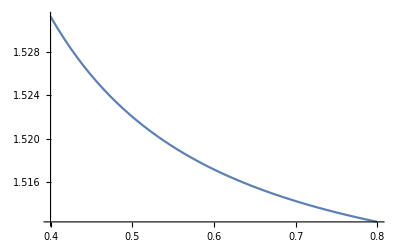

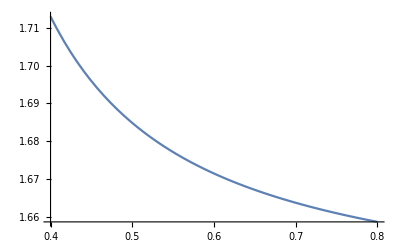

```mathematica
Plot[nBK7[λ],{λ,.4,.8}]
Plot[nSF5[λ],{λ,.4,.8}]
```

2. Design an achromatic doublet using this combination of crown and flint glasses for a total focal length F_d = 100 mm of the doublet and compute the residual chromatic aberration over the visible region.

```mathematica
nd=.58756;nF=.48613;nC=.65627;Fd=100;
```

```mathematica
V1d=VBK7=(nBK7[nd]-1)/(nBK7[nF]-nBK7[nC])
V2d=VSF5=(nSF5[nd]-1)/(nSF5[nF]-nSF5[nC])
```

68.4231

32.2507

```mathematica
F1d=Fd*(V1d-V2d)/V1d
F2d=Fd*(V2d-V1d)/V2d
```

52.8659

-112.16

From lecture notes: ‘Typically, in design of achromatic doublets, one uses positive a crown element and a negative flint element.’ This follows the results above.

```mathematica
FTotal=(1/F1d+1/F2d)^-1
```

100.

```mathematica
F[λ_] :=((nBK7[λ]-1)/(nBK7[nd]-1)*1/F1d+(nSF5[λ]-1)/(nSF5[nd]-1)*1/F2d)^-1
```

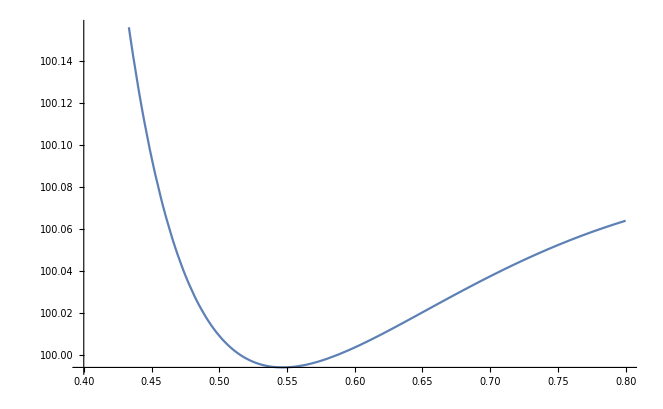

```mathematica
Plot[F[λ],{λ,.4,.8}]
```

3. Repeat the design for a hybrid refractive-diffractive achromat with either a BK7 or SF5 refractive element and analyze the resulting residual chromatic aberrations. Compare the results in all three cases.

```mathematica
V1d=VBK7=(nBK7[nd]-1)/(nBK7[nF]-nBK7[nC])
V2dH=-3.452;
```

68.4231

```mathematica
F1dH=Fd*(V1d-V2dH)/V1d
F2dH=Fd*(V2dH-V1d)/V2dH
```

105.045

2082.13

```mathematica
FTotal=(1/F1dH+1/F2dH)^-1
```

100.

```mathematica
F[λ_] :=((nBK7[λ]-1)/(nBK7[nd]-1)*1/F1dH+(nSF5[λ]-1)/(nSF5[nd]-1)*1/F2dH)^-1
```

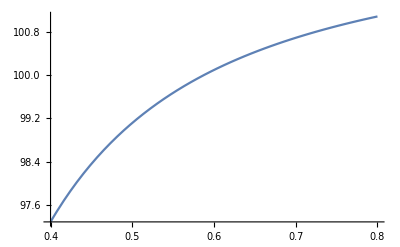

```mathematica
Plot[F[λ],{λ,.4,.8}]
```

TakeawaysPlotting all of these we can see that the Hybrid is easier to build, but is less effective across a wide spectrum

## Problem 3: Design of direct-view transmission grisms

Consider the illustration below, which shows an optical prism with a grating of period d fabricated on its back surface (called a grism).

-Graphics-

The incident rays at all wavelengths propagate horizontally, and light is refracted by the first surface according to Snell’s law. Then the rays are diffracted by the grating according to the grating equation, which for the first diffraction order reads as

							n’(λ) sin I’(λ) = n(λ) sin I(λ) + λ/d,

where we have explicitly indicated the wavelength dependence of the refractive indices before and after the grating, n(λ) and n′(λ), as well as that of the angles of incidence and diffraction I(λ) and I’(λ).

1. Derive a condition between d and α, which ensures the direct-view condition I’(λ_0) = 0 at some design wavelength λ_0. Be careful with the sign conventions to get positive values for d.

```mathematica
d=λ/(n2*Sin[α-ArcSin[n1/n2 Sin[α]]]);
```

2. Assuming that λ0 = λd = 0.5876 μm, plot the wavelength dependence of the angle of diffraction I’(λ) for some different values of α, such as 15◦, 30◦, and 45◦, over the visible region. Use the refractive-index data of BK7 for n(λ).

```mathematica
n1=1;n3=n1;α1=π/12;α2=π/6;α3=π/4;λd=0.5876;
```

```mathematica
d=λd/(nBK7[λd]*Sin[α-ArcSin[n1/nBK7[λd] Sin[α]]])
```

{4.28766,2.07302,1.30709}

```mathematica
Plot[{ArcSin[nBK7[λ]/n1*Sin[α1-ArcSin[n1/nBK7[λ] Sin[α1]]]+λ/(λd/(nBK7[λd]*Sin[α1-ArcSin[n1/nBK7[λd] Sin[α1]]]))],ArcSin[nBK7[λ]/n1*Sin[α2-ArcSin[n1/nBK7[λ] Sin[α2]]]+λ/(λd/(nBK7[λd]*Sin[α2-ArcSin[n1/nBK7[λd] Sin[α2]]]))],ArcSin[nBK7[λ]/n1*Sin[α2-ArcSin[n1/nBK7[λ] Sin[α2]]]+λ/(λd/(nBK7[λd]*Sin[α3-ArcSin[n1/nBK7[λd] Sin[α3]]]))]},{λ,.4,.8},PlotLegends->Automatic]
```

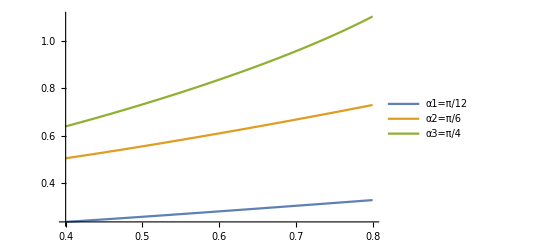

## Problem 4: Spherical aberration of hybrid achromatic doublets

Consider again the thin hybrid refractive-diffractive achromat made with BK7 glass, with focal length 100 mm and the object at infinity. Evaluate the Seidel sum for spherical aberration by adding the Seidel coefficients of thin refractive and diffractive lenses. Compare the following cases:

1. Optimized bending parameters for both refractive and diffractive elements. What are the optimum bending parameter values?

For spherical aberrations, we should consider Seidel coefficient S_I and find the optimizing for the bending parameter by taking the derivative. Setting this derivative = 0 will give us the optimized bending parameter for this situation. 

						For refractive element: (∂S_I)/(∂B)=(2(n+2)B)/(n(n-1))^2-(4(n+1))/(n(n-1))=0⟹(2(n+2)B)/(n(n-1))^2=(4(n+1))/(n(n-1))⟹B=(4(n+1)(n-1))/(2(n+2))
						For diffractive element:(∂S_I)/(∂D)=2D-4=0⟹D=2

```mathematica
B1=B=(4(nBK7[λd]+1)(nBK7[λd]-1))/(2(nBK7[λd]+2))
```

0.740995

2. Optimized bending at the refractive element only, with a flat diffractive element.

For the refractive lens we have already solved above. So, we only need to solve for the diffractive element. As a flat surface the curvature, c = 0. Therefore, we simply requie the bening parameter for the refractive element as

							D=2*c*f=0

```mathematica
B2=B+0
```

0.740995

3. Cemented element with a flat diffractive back surface.

Again we have already solved for the refractive element, but we will have to solve for the cemented flat diffractive lens where again c_2 = 0.

							B = (c_1+c_2)/(c_1-c_2)=c_1/c_1=1

```mathematica
B3=B+1
```

1.74099

4. A purely refractive singlet with optimized bending.

We have already used the refractive element many times, and now it is the only lens in the system, and the only componet to be minimized therefore,

```mathematica
B4=B
```

0.740995

## Problem 5: Lommel theory of annular pupils

Suppose that the circular pupil has a central obstruction (as is usual in Cassegrain-type telescopes) to that 

							t(k_ρ) = 1 when kcΘ ≤ k_ρ ≤ kΘ.02

and t(k_ρ) = 0 otherwise. Using Lommel’s theory, show that the diffraction pattern in the focal plane (optical coordinate u = 0) takes the form

							V(v,0) = V(0,0) 2/(1-c^2) (J_1(v)-cJ_1(c*v))/v

Plot the resulting intensity profile for different values of c and investigate the limiting case of a ring aperture with c ⟶ 1. Evaluate the result in this limiting case also for an arbitrary value of u.

```mathematica
-Graphics-
-Graphics-
```

```mathematica
V00=1;c1=0;c2=0.5;c3=0.9;c4=0.99;c={0,.5,.99};V0=1;
```

```mathematica
Plot[{Abs[V00*2/(1-c1^2)*(BesselJ[1,v]-c1*BesselJ[1,c1*v])/v]^2,Abs[V00*2/(1-c2^2)*(BesselJ[1,v]-c2*BesselJ[1,c2*v])/v]^2,Abs[V00*2/(1-c3^2)*(BesselJ[1,v]-c3*BesselJ[1,c3*v])/v]^2,Abs[V00*2/(1-c4^2)*(BesselJ[1,v]-c4*BesselJ[1,c4*v])/v]^2},{v,0,10},PlotLegends->Automatic]
```

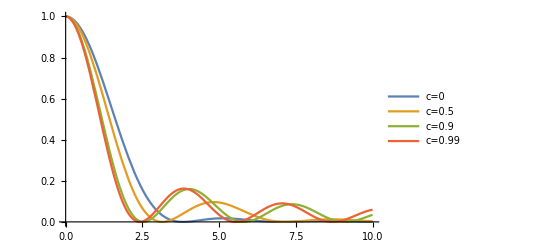

## Problem 6: Incoherent images of gratings

Let us suppose that the extended object in an incoherent imaging system is a grating with period d and a a y-invariant intensity transmittance

							I_O(x) =1/2[1 + cos(2πx/d)] .

The pupil function of the system is assumed to be Gaussian,

							t(k_x, k_y) =1/(π*k*ω)exp((k_x^2+k_y^2)/(k^2 ω^2))

The Lommel theory can be used if the system is paraxial, i.e., if w ≤ 1.Apply this theory to show that the image-plane intensity distribution is of the form

							I(x)=ω^2/(4π){1+exp[-(λ/d)/(2 ω^2)]cos(2πx/d)}

Plot these distributions for different values of d/λ assuming, e.g., that w = 0.1.

```mathematica
-Graphics--Graphics--Graphics--Graphics--Graphics-
```

```mathematica
nd=.58756;nF=.48613;nC=.65627;λ={nF,nd,nC};d1=1;d2=2;d3=4;d4=16;d5=64;ω=0.1;
```

```mathematica
Plot[{ω^2/(4π)(1+Exp[-(λ/d1)^2/(2 ω^2)]*Cos[2π*x/d1]),ω^2/(4π)(1+Exp[-(λ/d2)^2/(2 ω^2)]*Cos[2π*x/d2]),ω^2/(4π)(1+Exp[-(λ/d3)^2/(2 ω^2)]*Cos[2π*x/d3]),ω^2/(4π)(1+Exp[-(λ/d4)^2/(2 ω^2)]*Cos[2π*x/d4]),ω^2/(4π)(1+Exp[-(λ/d5)^2/(2 ω^2)]*Cos[2π*x/d5])},{x,-10,10},PlotLegends->Automatic]
```